```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
(*this is the length of the one-dimensional mesh[1]*)
L1=1.2444414542953002;
r=0.2;
cr={0.45,0.55};
NN=13;
Δθ=2π/NN;
Δl=2 r Sin[Δθ/2];
```

```mathematica
(*test case 1*)
```

```mathematica
u2d[x_]:=1+x[[1]]^2 + 2 x[[2]]^2
```

```mathematica
tabr=Table[cr +r{Cos[n Δθ],Sin[n Δθ]},{n,0,NN}];
```

```mathematica
tabr
```

{{0.65,0.55},{0.627091,0.642945},{0.563613,0.714597},{0.474107,0.748542},{0.379079,0.737003},{0.300298,0.682625},{0.255812,0.597863},{0.255812,0.502137},{0.300298,0.417375},{0.379079,0.362997},{0.474107,0.351458},{0.563613,0.385403},{0.627091,0.457055},{0.65,0.55}}

```mathematica
plot2d={};
For[i=1,i<=NN,i++,
AppendTo[plot2d,Plot[u2d[tabr[[i]]+(s-(i-1)Δl)/Δl *(tabr[[i+1]]-tabr[[i]])],{s,(i-1)Δl,i Δl}]];
]
```

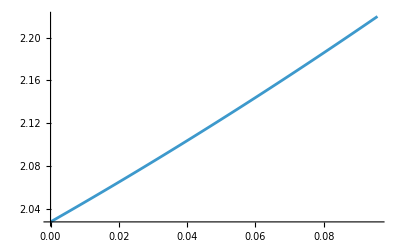
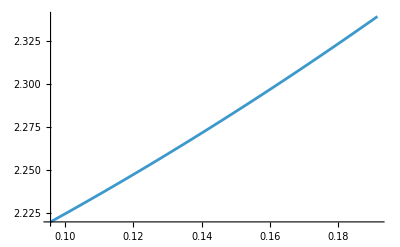
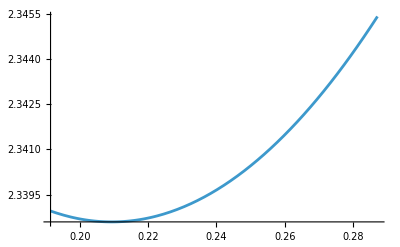
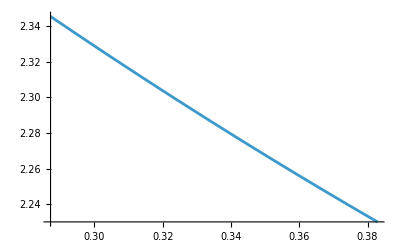
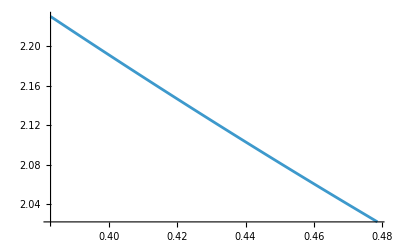
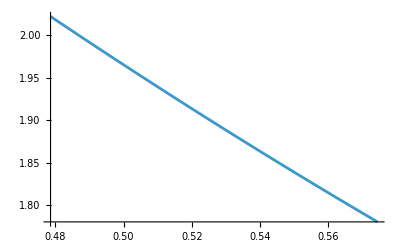
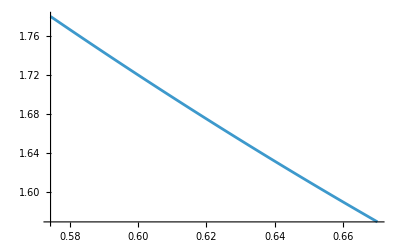
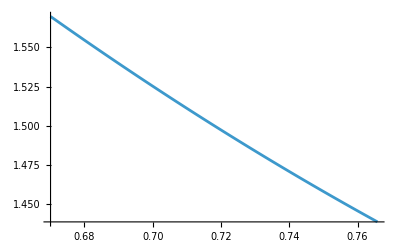

```mathematica
plot2d
```

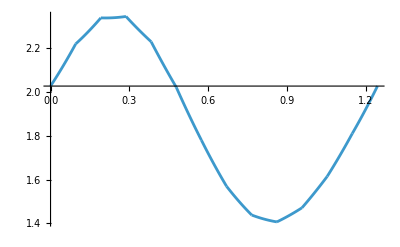

```mathematica
plot2d=Show[plot2d,PlotRange->Full]
```

```mathematica
tline=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_line.csv"][[2;;]];
tline=Table[{tline[[i,2]],tline[[i,1]]},{i,2,Length[tline]}]
```

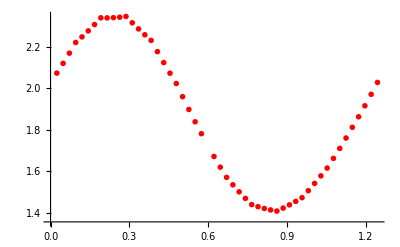

```mathematica
plottline=ListPlot[tline,PlotStyle->{Red,PointSize->0.01}]
```

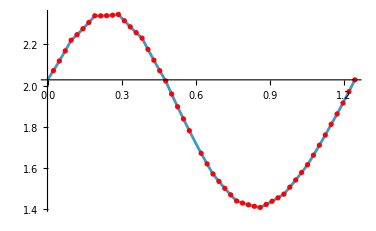

```mathematica
Show[plot2d,plottline]
```